```mathematica
x=Import["https://coinmarketcap.com/currencies/ethereum/","Data"];
```

```mathematica
x1=((x[[5,1]][[2,2]])[[2,2]]);
```

```mathematica
Cases[x1,{_,_,"ETH/USD"|"ETH/USDT",__}]//MatrixForm
```

```mathematica
date=(First@DateObject[])[[1;;-4]]
```

{2018,10,9}

```mathematica
(StringLength/@(ToString/@date))
```

{4,2,1}

```mathematica
{2018,10,9}
```

```mathematica
data=Import["https://coinmarketcap.com/currencies/ethereum/historical-data/?start=20180901&end=20181009","Data"];
```

```mathematica
da=Join[{((data[[5,1]])[[2,2]][[1]])},((data[[5,1]])[[2,2]][[2]])];
```

```mathematica
da[[1;;5]]//MatrixForm
```

(Date | Open* | High | Low | Close** | Volume | Market Cap
Oct 08, 2018 | 226.51 | 230.76 | 224.56 | 229.25 | 1,470,740,000 | 23,201,746,333
Oct 07, 2018 | 225.44 | 226.37 | 223. | 226.12 | 1,470,480,000 | 23,087,109,194
Oct 06, 2018 | 227.55 | 227.93 | 224.25 | 225.12 | 1,505,070,000 | 23,299,225,467
Oct 05, 2018 | 222.27 | 228.32 | 220.96 | 227.6 | 1,547,330,000 | 22,753,560,914)

```mathematica
traindata=da[[2;;,2;;]];
```

```mathematica
in=traindata[[All]];
```

```mathematica
out=traindata[[All,4]];
```

```mathematica
train=Thread[Rest[in]->Most[out]];
```

```mathematica
train[[1;;3]]//MatrixForm
```

({225.44,226.37,223.,226.12,1,470,480,000,23,087,109,194}→229.25
{227.55,227.93,224.25,225.12,1,505,070,000,23,299,225,467}→226.12
{222.27,228.32,220.96,227.6,1,547,330,000,22,753,560,914}→225.12)

```mathematica
train=RandomSample@train;
```

```mathematica
train//Length
```

37

```mathematica
p=Predict[train[[1;;-11]],ValidationSet->train[[-10;;]],Method->{"GradientBoostedTrees",MaxTrainingRounds->100}]
```

PredictorFunction[…]

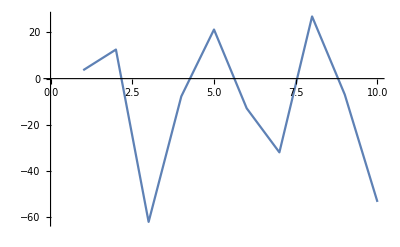

```mathematica
Thread[p[Keys@train[[-10;;]]]-Values@train[[-10;;]]]//ListLinePlot
```

```mathematica
pm=PredictorMeasurements[p,train[[-10;;]]]
```

PredictorMeasurementsObject[…]

```mathematica
Sqrt@pm["MeanSquare"]
```

8.5333

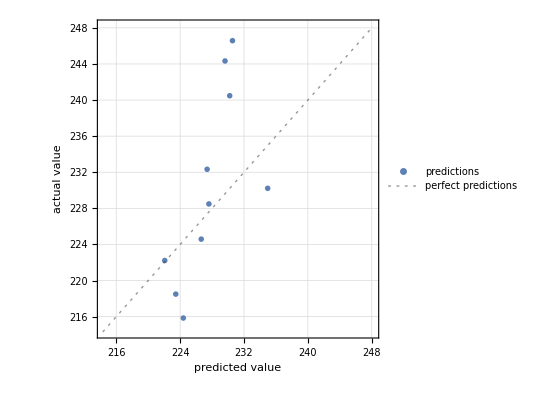

```mathematica
pm["ComparisonPlot"]
```

```mathematica
p=Predict[train[[1;;-101]],ValidationSet->train[[-100;;]],Method->{"GradientBoostedTrees","BoostingMethod"->"Gradient","LeafSize"->20,"LeavesNumber"->50,"MaxDepth"->6,MaxTrainingRounds->1000}]
```